```mathematica
3-mode Quantum Transducer Coupling
```

```mathematica
Shoumik Chowdhury  5/12/2020
```

## Preliminaries

```mathematica
Id[n_]:=IdentityMatrix[n]
mJn[n_]:=ArrayFlatten[Id[n]⊗({{0, 1}, {-1, 0}})](*Symplectic matrix in QP basis*)
mJqqn[n_]:=ArrayFlatten[({{0, 1}, {-1, 0}})⊗Id[n]](*Symplectic matrix in QQ basis*)
sympQn[mS_,n_]:=1-Norm[mSᵀ.mJn[n].mS-mJn[n]](*Test for symplecticity*)
n=6;(*For a 3-mode transducer we work with n=6*)
mJ=mJn[n];
sympQ[mS_]:=sympQn[mS,n]
```

```mathematica
QQtoQP[n0_, M0_] :=
(* Converts a matrix from QQ basis to QP basis*) 
Module[{n=n0, M=M0},
	ord= Flatten[Table[{i, n+i}, {i, 1, n}]];
	Return[M⟦ord, ord⟧]
]

QPtoQQ[n0_, M0_] := 
(* Converts a matrix from QP basis to QQ basis*)
Module[{n=n0, M=M0},
	odds = Table[{i}, {i, 1, 2n, 2}];
	evens = Table[{i+1}, {i, 1, 2n, 2}];
	ord = Flatten[Join[odds,evens]];
	Return[M⟦ord, ord⟧]
] 

(*Generate random n×n symplectic matrix in QQ basis and convert to QP*)
rSymMat[{a_,b_},c_]:=(UpperTriangularize[#]+UpperTriangularize[#,1]ᵀ)&@RandomReal[{a,b},{c,c}];
rSympMat[a_,b_, n_]:=QQtoQP[n, Id[2n]-Inverse[(mJqqn[n].rSymMat[{a,b},2n]+1/2 Id[2n])]]; 
(*Generate random local operations for n = 6*)
randomLocal[a_, b_] := ArrayFlatten[({{rSympMat[a,b, 1], 0, 0, 0, 0, 0}, {0, rSympMat[a,b, 1], 0, 0, 0, 0}, {0, 0, rSympMat[a,b, 1], 0, 0, 0}, {0, 0, 0, rSympMat[a,b, 1], 0, 0}, {0, 0, 0, 0, rSympMat[a,b, 1], 0}, {0, 0, 0, 0, 0, rSympMat[a,b, 1]}})];
```

## Theory

References:"Cavity Optomechanics" (https: //arxiv.org/abs/1303.0733) and KL paper (https: //www.nature.com/articles/nphys2911)
Hamiltonian given by   (a⃗)^†.H.a⃗, where  a⃗ = {a_o, a_m, a_μ, a_o^†, a_m^†, a_μ^†} and  (a⃗)^†= {(a_o)^†,(a_m)^†,(a_μ)^†,a_o,a_m,a_μ}
H = 1/2(Δ_o | g_om | 0 | 0 | g_om | 0
g_om | ω_m | g_μm | g_om | 0 | g_μm
0 | g_μm | Δ_μ | 0 | g_μm | 0
0 | g_om | 0 | Δ_o | g_om | 0
g_om | 0 | g_μm | g_om | ω_m | g_μm
0 | g_μm | 0 | 0 | g_μm | Δ_μ) := (A | B
B^† | P)
Linearized Hamiltonian:H=Δ_o ((a_o)^† a_o+1/2)+Δ_μ ((a_μ)^† a_μ+1/2)+ω_m ((a_m)^† a_m+1/2)+g_om (a_o+(a_o)^†) (a_m+(a_m)^†)+g_μm (a_μ+(a_μ)^†) (a_m+(a_m)^†)   
Langevin Eq: d/dt (a
a^†)= I [(a | a^†)H(a
a^†), (a
a^†)] - 1/2(κ | 0
0 | κ)(a
a^†)+(√κ | 0
0 | √κ)(A_in
A_in^†) (*1mode example *)
Fourier Transform: â[ω] ∝∫â(t) e^(-I ω t)dt       and     (â[-ω])^† ∝∫â (t)^† e^(-I ω t)dt
Langevin → (I ω | □
□ | Iω)(a[ω]
a[-ω]^†)= I(-A^⋆-P | -B^†
B^ᵀ | A+P^⋆)(a[ω]
a[-ω]^†)- 1/2(κ | 0
0 | κ)(a[ω]
a[-ω]^†) + (√κ | 0
0 | √κ)(A_in[ω]
A_in[-ω]^†)
Thus →    T(a[ω]
a[-ω]^†) = Y(A_in[ω]
A_in[-ω]^†); then extend this to a[-ω] and a[ω]^†modes to get full matrix
Input Output relation: A_out[ω] = A_in[ω] - √κ a[ω]; gives matrix equations (A⃗)_out[ω] = (A⃗)_in[ω] - W(M^-1 W  (A⃗)_in)= S_complex(A⃗)_in

## Setup and Initialization

```mathematica
generateMS[Δo_,ωm_,Δμ_, gom_,gμm_,goμ_]:= 
Module[{κo=1,κm=1,κμ=1,κb=1},
T[ω0_]:=I ({{ω0, 0, 0, 0, 0, 0}, {0, ω0, 0, 0, 0, 0}, {0, 0, ω0, 0, 0, 0}, {0, 0, 0, ω0, 0, 0}, {0, 0, 0, 0, ω0, 0}, {0, 0, 0, 0, 0, ω0}})- I({{-Δo+(ⅈ κo)/2, -gom, -goμ, 0, -Conjugate[gom]/2, 0}, {-Conjugate[gom], -ωm+(ⅈ κm)/2, -gμm, -Conjugate[gom]/2, 0, -Conjugate[gμm]/2}, {-Conjugate[goμ], -Conjugate[gμm], -Δμ+(ⅈ κμ)/2, 0, -Conjugate[gμm]/2, 0}, {0, gom/2, 0, Δo+(ⅈ κo)/2, Conjugate[gom], Conjugate[goμ]}, {gom/2, 0, gμm/2, gom, ωm+(ⅈ κm)/2, Conjugate[gμm]}, {0, gμm/2, 0, goμ, gμm, Δμ+(ⅈ κμ)/2}});
M:=({{T[ω], 0}, {0, T[-ω]}})//ArrayFlatten;
Y=({{√Subscript[κ, o], 0, 0, 0, 0, 0}, {0, √Subscript[κ, m], 0, 0, 0, 0}, {0, 0, √Subscript[κ, μ], 0, 0, 0}, {0, 0, 0, √Subscript[κ, o], 0, 0}, {0, 0, 0, 0, √Subscript[κ, m], 0}, {0, 0, 0, 0, 0, √Subscript[κ, μ]}});
W=({{Y, 0}, {0, Y}})//ArrayFlatten;
U=1/(√2)({{1, ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, ⅈ, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, ⅈ, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, -ⅈ, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, -ⅈ, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -ⅈ}, {0, 0, 0, 0, 0, 0, 1, ⅈ, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, ⅈ, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, ⅈ}, {1, -ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, -ⅈ, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, -ⅈ, 0, 0, 0, 0, 0, 0}});
SComplex=Id[12]-W.Inverse[M[ω]].W;
Inverse[U].SComplex.U
]

DecoupleQ[mS_,n_,mode_]:=
(*This is a wrapper function to compute the local operations given input mS.We rotate column c->row r*)Module[{cv,rv,ncv,nrv,mL,c=2 mode-1,r=2 mode-1},(*Tabular representations of column vector cv and row vectow rv in qpqp basis*)cv=Table[{mS[[i,c]],mS[[i+1,c]]},{i,1,2 n,2}];
rv=Table[{mS[[r,i]],mS[[r,i+1]]},{i,1,2 n,2}];
(*we are going to rotate column c->row r*)
ncv=Norm/@cv/.0->1;(*list of norms of cv*)
nrv=Norm/@rv/.0->1;(*list of norms of rv*)
mL=
Table[(({{rv⟦i,1⟧, -rv⟦i,2⟧}, {rv⟦i,2⟧, rv⟦i,1⟧}})/nrv⟦i⟧).({{nrv⟦i⟧/ncv⟦i⟧, 0}, {0, ncv⟦i⟧/nrv⟦i⟧}}).(({{cv⟦i,1⟧, cv⟦i,2⟧}, {-cv⟦i,2⟧, cv⟦i,1⟧}})/ncv⟦i⟧),{i,1,n}]/.({{0, 0}, {0, 0}})->({{1, 0}, {0, 1}}) ;(*List of local symplectic operations for all modes*)ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@mL]]
]

DecoupleP[mS_,n_,mode_]:=
(*This is a wrapper function to compute the local operations given input mS.We rotate column c->row r*)Module[{cv,rv,ncv,nrv,mL,c=2 mode,r=2 mode},(*Tabular representations of column vector cv and row vectow rv in qpqp basis*)cv=Table[{mS[[i,c]],mS[[i+1,c]]},{i,1,2 n,2}];
rv=Table[-{mS[[r,i]],mS[[r,i+1]]},{i,1,2 n,2}];
rv[[mode,1]]=-rv[[mode,1]];(*we are going to rotate column c->row r*)
ncv=Norm/@cv/.0->1;nrv=Norm/@rv/.0->1;
mL=
Table[(({{rv⟦i,1⟧, -rv⟦i,2⟧}, {rv⟦i,2⟧, rv⟦i,1⟧}})/nrv⟦i⟧).({{nrv⟦i⟧/ncv⟦i⟧, 0}, {0, ncv⟦i⟧/nrv⟦i⟧}}).(({{cv⟦i,1⟧, cv⟦i,2⟧}, {-cv⟦i,2⟧, cv⟦i,1⟧}})/ncv⟦i⟧),{i,1,n}]/.({{0, 0}, {0, 0}})->({{1, 0}, {0, 1}});
mL[[mode]]=-mL[[mode]];
]







ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@mL]]]
```

```mathematica
T[ω_] := I({{ω, 0, 0, 0, 0, 0}, {0, ω, 0, 0, 0, 0}, {0, 0, ω, 0, 0, 0}, {0, 0, 0, ω, 0, 0}, {0, 0, 0, 0, ω, 0}, {0, 0, 0, 0, 0, ω}}) - I({{- Δo_+I κo/2, -gom, -goμ, 0, -gom/2, 0}, {-gom, - ωm+I κm/2, -gμm, -gom/2, 0, -gμm/2}, {-goμ, -gμm, - Δμ+I κμ/2, 0, -gμm/2, 0}, {0, Subscript[g, om]/2, 0, Δo+ I κo/2, Subscript[g, om], Subscript[g, oμ]}, {Subscript[g, om]/2, 0, Subscript[g, μm]/2, Subscript[g, om], ωm+I κm/2, Subscript[g, μm]}, {0, Subscript[g, μm]/2, 0, Subscript[g, oμ], Subscript[g, μm], Δμ+ I κμ/2}});
M:=({{T[ω], 0}, {0, T[-ω]}})//ArrayFlatten;
```

```mathematica
M[ω_] := ({{T[ω], 0}, {0, T[-ω]}}) // ArrayFlatten
```

```mathematica
Y = ({{√Subscript[κ, o], 0, 0, 0, 0, 0}, {0, √Subscript[κ, m], 0, 0, 0, 0}, {0, 0, √Subscript[κ, μ], 0, 0, 0}, {0, 0, 0, √Subscript[κ, o], 0, 0}, {0, 0, 0, 0, √Subscript[κ, m], 0}, {0, 0, 0, 0, 0, √Subscript[κ, μ]}});
W = ({{Y, 0}, {0, Y}}) // ArrayFlatten;
SComplex=Id[12]-W.Inverse[M[ω]].W;
```

```mathematica
Setting values
```

```mathematica
{Subscript[Δ, o], ωm, Subscript[Δ, μ], Subscript[κ, o], Subscript[κ, μ], Subscript[κ, m]} = {5, 1, 4, 1, 1, 1} 
{Subscript[g, om],Subscript[g, μm], Subscript[g, oμ]} = {17,23, 0}
```

{5,1,4,1,1,1}

{17,23,0}

```mathematica
Finding Scattering Matrices
```

```mathematica
(SComplex= Id[12] - W.Inverse[M[ω]].W );
```

We want to change from basis A to basis B
(A) ao[+ω], am[+ω],aμ[+ω],(ao[-ω])^†,(am[-ω])^†,(aμ[-ω])^†,ao[-ω],am[-ω],aμ[-ω], ...
(B) qo[+ω], po[+ω],qm[+ω], pm[+ω], qμ[+ω], pμ[+ω],qo[-ω], po[-ω], ...

```mathematica
(S = Inverse[U].SComplex.U);
```

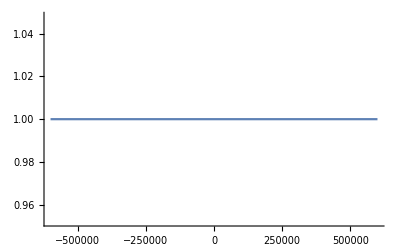

```mathematica
Plot[N[sympQ[S/.{ω->x}]] , {x, -600000, 600000}](* evaluate this numerically? *)
```

#### Symplectic Decoupling Algorithm

#### Part 1: Code to Decouple the first quadrature

```mathematica
Decouple1Q[mS0_, n0_, c0_, r0_] := 
(*This is a wrapper function to compute the local operations given input mS. We rotate column c -> row r *) 
Module[{mS = mS0, n=n0, c=c0, r =r0},
(* Tabular representations of column vector cv and row vectow rv in qpqp basis *)
cv=Table[{mS⟦i,c⟧,mS⟦i+1,c⟧},{i,1,2n, 2}];
rv=Table[{mS⟦r,i⟧,mS⟦r,i+1⟧},{i,1,2n, 2}];
(*we are going to rotate column c -> row r*)

ncv=Norm/@cv;  /. 0 -> 1; (*list of norms of cv*)
nrv=Norm/@rv /. 0 -> 1;(*list of norms of rv*)
mL=Table[(({{rv⟦i,1⟧, -rv⟦i,2⟧}, {rv⟦i,2⟧, rv⟦i,1⟧}})/nrv⟦i⟧).({{nrv⟦i⟧/ncv⟦i⟧, 0}, {0, ncv⟦i⟧/nrv⟦i⟧}}).(({{cv⟦i,1⟧, cv⟦i,2⟧}, {-cv⟦i,2⟧, cv⟦i,1⟧}})/ncv⟦i⟧),{i,1,n}] /. ({{0, 0}, {0, 0}}) -> ({{1, 0}, {0, 1}}); 
(*List of local symplectic operations for all modes*)

mSL1qq=ArrayFlatten[({{DiagonalMatrix[mL⟦;;,1,1⟧], DiagonalMatrix[mL⟦;;,1,2⟧]}, {DiagonalMatrix[mL⟦;;,2,1⟧], DiagonalMatrix[mL⟦;;,2,2⟧]}})]; (*this gives a result in qqpp*)

mSL1 = QQtoQP[n, mSL1qq];
Return[mSL1]
]
```

```mathematica
Part 2: Code to Decouple the second quadrature
```

```mathematica
(* INSERT THE CODE HERE *)
```

```mathematica
Plotter[mS0_] := 
Module[{mS = mS0}, 
mSL1=Decouple1Q[mS,n,9,9];
mS1=Re[mS.mJ.mSL1.mS];
newSC = U.mS1.Inverse[U];
newM = Inverse[Id[12] - newSC];

Im[Chop[N[newM⟦1, 2⟧], 10^-8]]
]
```

```mathematica
{Subscript[Δ, o],ωm,Subscript[Δ, μ],Subscript[κ, o],Subscript[κ, μ],Subscript[κ, m]}={3,1,5,1,1,1};
{Subscript[g, om],Subscript[g, μm],Subscript[g, oμ]}={17,23,0};
```

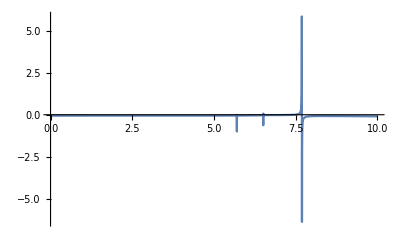

```mathematica
Plot[N[Plotter[S /. {ω -> x}]], {x, 0, 10}, PlotRange->Full]
```

```mathematica
Re[S /. {ω -> 1.}] // MatrixForm
```

(0.994882 | -0.0578826 | -0.00017123 | -0.05385 | 0.0028498 | 0.0731819 | -0.000296908 | -0.018184 | -0.000550578 | 0.0312123 | 0.000574935 | -0.00988958
0.0578826 | 0.994882 | 0.05385 | -0.00017123 | -0.0731819 | 0.0028498 | -0.018184 | 0.000296908 | 0.0312123 | 0.000550578 | -0.00988958 | -0.000574935
-0.00017123 | -0.05385 | 0.998458 | 0.0307835 | 0.00139917 | -0.0364959 | 0.00119395 | 0.0345025 | -0.0000371251 | -0.0235451 | -0.000748349 | 0.0187901
0.05385 | -0.00017123 | -0.0307835 | 0.998458 | 0.0364959 | 0.00139917 | 0.0345025 | -0.00119395 | -0.0235451 | 0.0000371251 | 0.0187901 | 0.000748349
0.0028498 | 0.0731819 | 0.00139917 | -0.0364959 | 0.996406 | -0.0335175 | -0.000712849 | -0.0123139 | 0.000505139 | 0.0211663 | 0.000111333 | -0.00671778
-0.0731819 | 0.0028498 | 0.0364959 | 0.00139917 | 0.0335175 | 0.996406 | -0.0123139 | 0.000712849 | 0.0211663 | -0.000505139 | -0.00671778 | -0.000111333
0.000296908 | -0.018184 | -0.00119395 | 0.0345025 | 0.000712849 | -0.0123139 | 0.991738 | -0.0834914 | -0.00110868 | -0.0561868 | 0.00564039 | 0.0892697
-0.018184 | -0.000296908 | 0.0345025 | 0.00119395 | -0.0123139 | -0.000712849 | 0.0834914 | 0.991738 | 0.0561868 | -0.00110868 | -0.0892697 | 0.00564039
0.000550578 | 0.0312123 | 0.0000371251 | -0.0235451 | -0.000505139 | 0.0211663 | -0.00110868 | -0.0561868 | 0.998627 | 0.0250256 | 0.0016726 | -0.0305656
0.0312123 | -0.000550578 | -0.0235451 | -0.0000371251 | 0.0211663 | 0.000505139 | 0.0561868 | -0.00110868 | -0.0250256 | 0.998627 | 0.0305656 | 0.0016726
-0.000574935 | -0.00988958 | 0.000748349 | 0.0187901 | -0.000111333 | -0.00671778 | 0.00564039 | 0.0892697 | 0.0016726 | -0.0305656 | 0.994462 | -0.0510309
-0.00988958 | 0.000574935 | 0.0187901 | -0.000748349 | -0.00671778 | 0.000111333 | -0.0892697 | 0.00564039 | 0.0305656 | 0.0016726 | 0.0510309 | 0.994462)

```mathematica
mS = S  /. {ω -> 3.};
mSL1 = Decouple1Q[mS, n, 9, 9];
mS1 = Re[mS.mJ.mSL1.mS];
{sympQ[mSL1], sympQ[mS1]}
Eigenvalues[mSL1.Transpose[mSL1]]
(Chop[N[mS1], 10^-8]) // MatrixForm
Scomp1=U.mS1.Inverse[U];
newM=Inverse[Id[12]-Scomp1];
Im[Chop[N[newM[[1;;6,1;;6]]],10^-8]]//MatrixForm
```

{1.,1.}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

(0.0639259 | 0.984527 | 0.108731 | 0.00405827 | -0.129325 | 0.005458 | -0.0413905 | 0.00691575 | 0 | 0 | -0.0146 | -0.000248282
-0.984527 | 0.0639259 | -0.00405827 | 0.108731 | -0.005458 | -0.129325 | 0.00691575 | 0.0413905 | 0 | 0 | -0.000248282 | 0.0146
0.108731 | 0.00405827 | -0.074129 | 0.991672 | 0.0840574 | 0.00538925 | 0.0830444 | -0.00996624 | 0 | 0 | 0.029046 | 0.00183583
-0.00405827 | 0.108731 | -0.991672 | -0.074129 | -0.00538925 | 0.0840574 | -0.00996624 | -0.0830444 | 0 | 0 | 0.00183583 | -0.029046
-0.129325 | 0.005458 | 0.0840574 | 0.00538925 | 0.0782447 | 0.985501 | -0.0318869 | 0.00620777 | 0 | 0 | -0.0113033 | 0.000109824
-0.005458 | -0.129325 | -0.00538925 | 0.0840574 | -0.985501 | 0.0782447 | 0.00620777 | 0.0318869 | 0 | 0 | 0.000109824 | 0.0113033
0.0413905 | 0.00691575 | -0.0830444 | -0.00996624 | 0.0318869 | 0.00620777 | -0.152767 | -0.963041 | 0 | 0 | 0.231924 | -0.0723721
0.00691575 | -0.0413905 | -0.00996624 | 0.0830444 | 0.00620777 | -0.0318869 | 0.963041 | -0.152767 | 0 | 0 | 0.0723721 | 0.231924
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0
0.0146 | -0.000248282 | -0.029046 | 0.00183583 | 0.0113033 | 0.000109824 | 0.231924 | -0.0723721 | 0 | 0 | -0.408096 | -0.880693
-0.000248282 | -0.0146 | 0.00183583 | 0.029046 | 0.000109824 | -0.0113033 | 0.0723721 | 0.231924 | 0 | 0 | 0.880693 | -0.408096)

(-0.540612 | -0.0528144 | 0.0687819 | 0.0180821 | 0 | 0.00685392
-0.0528144 | -0.466746 | -0.0395621 | -0.0378419 | 0 | -0.0143437
0.0687819 | -0.0395621 | -0.547305 | 0.0135449 | 0 | 0.00513412
-0.0180821 | 0.0378419 | -0.0135449 | -0.433269 | 0 | -0.0959844
0 | 0 | 0 | 0 | 0.5 | 0
-0.00685392 | 0.0143437 | -0.00513412 | -0.0959844 | 0 | -0.328126)